## Las funciones de las fórmulas (A1.6) figuran a continuación

### Definiciones

```mathematica
z[3][n_][z_]=SphericalHankelH1[n,z]
```

SphericalHankelH1[n,z]

```mathematica
R[3][1][n_][z_]=z[3][n][z]
```

SphericalHankelH1[n,z]

```mathematica
R[3][1][1.][1.]
```

0.301169-1.38177 ⅈ

#### Simplificación

```mathematica
FullSimplify[D[z SphericalHankelH1[n,z],{z,1}]/z]
```

((1+n) SphericalHankelH1[n,z])/z-SphericalHankelH1[1+n,z]

### Defininiciones (Cont.)

```mathematica
R[3][2][n_][z_]=((1+n) SphericalHankelH1[n,z])/z-SphericalHankelH1[1+n,z]
```

((1+n) SphericalHankelH1[n,z])/z-SphericalHankelH1[1+n,z]

### Gráficos

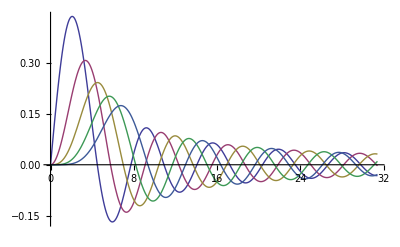

```mathematica
Plot[Evaluate[Table[Re[R[3][1][n][z]],{n,1,5}]],{z,0,10Pi},PlotRange->All]
```

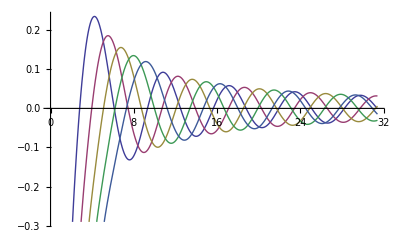

```mathematica
Plot[Evaluate[Table[Im[R[3][1][n][z]],{n,1,5}]],{z,0,10Pi}]
```

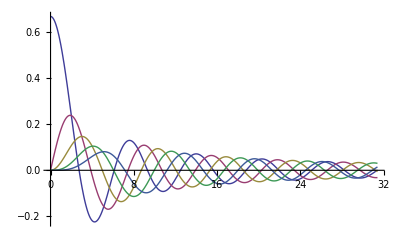

```mathematica
Plot[Evaluate[Table[Re[R[3][2][n][z]],{n,1,5}]],{z,0,10Pi},PlotRange->All]
```

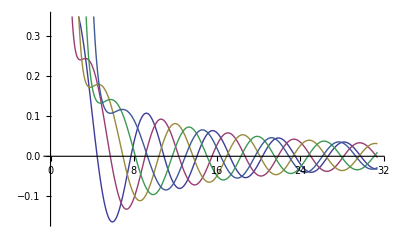

```mathematica
Plot[Evaluate[Table[Im[R[3][2][n][z]],{n,1,5}]],{z,0,10Pi}]
```

## En cuanto a las funciones de onda esféricas, dependen de una cierta normalización de los polinomios asociados de Legendre (ver (A1.25))

#### Tests

```mathematica
Limit[(x/Abs[x])^x,x->0]
```

1

```mathematica
Sign[0]
```

0

```mathematica
UnitStep[0]
```

1

```mathematica
Limit[(x/Abs[x])^x,x->-3]
```

-1

```mathematica
(2 UnitStep[x]-1)^x/.{x->-3}
```

-1

```mathematica
signm[m_]=If[m==0,1,(-Sign[m])^m]
```

If[m==0,1,(-Sign[m])^m]

```mathematica
signm[0]
```

1

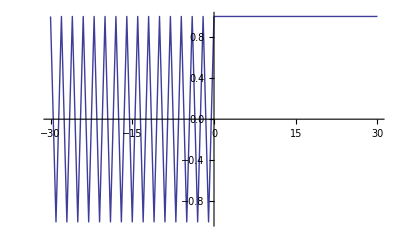

```mathematica
ListPlot[Table[{m,(2*UnitStep[m]-1)^m},{m,-30,30}],Joined->True]
```

### Definiciones (ver (A1.25))

```mathematica
signm[m_]=If[m==0,1,(-Sign[m])^m]
```

If[m==0,1,(-Sign[m])^m]

```mathematica
LegendrePbar[n_,m_,theta_]:=√(((2 n+1) (n-m)!)/(2 (n+m)!)) LegendreP[n,m,Cos[theta]]
```

```mathematica
LegendrePbarSin[n_,m_,theta_]:=√(((2 n+1) (n-m)!)/(2 (n+m)!)) LegendreP[n,m,Cos[theta]] Sin[theta]
```

```mathematica
LegendrePbarmInvSin[n_,m_,theta_]:=If[theta==0,
										If[Abs[m]==1,
											Sign[m] Sqrt[((2 n+1) (n-m)!)/(2 (n+m)!)]  n(n+1)/2,
											0],
										m LegendrePbar[n,m,theta]/Sin[theta]
										]
```

#### Simplificaciones

```mathematica
FullSimplify[D[LegendreP[n,m,Cos[theta]],{theta,1}]]
```

-(1+n) Cot[theta] LegendreP[n,m,Cos[theta]]+(1-m+n) Csc[theta] LegendreP[1+n,m,Cos[theta]]

```mathematica
Limit[Sin[theta](-(1+n) Cot[theta] LegendreP[n,m,Cos[theta]]+(1-m+n) Csc[theta] LegendreP[1+n,m,Cos[theta]]),theta->0]
```

Limit::ztest: Unable to decide whether numeric quantities RowBox[{"{", RowBox[{\(Abs[\(\(2\ \((\(-1\) - 1\/\(8192\ π\))\)\) + \(2\ \((1 + 1\/\(8192\ π\))\)\)\)]\), ",", \(Abs[\(\(1\/8192 - π\)\/\(2\ π\) + \(\(-\(1\/8192\)\) + π\)\/\(2\ π\)\)]\), ",", \(Abs[\(\(« 1 »\)\/\(« 1 »\) + \(« 1 »\)\)]\), ",", \(« 1 »\), ",", RowBox[{"Abs", "[", RowBox[{\(-1\), "+", \(2\ \((1\/2 - 1\/\(8192\ π\))\)\), "+", \(1\/\(4096\ π\)\), "+", FractionBox[RowBox[{\(-\(1\/4096\)\), "+", FractionBox[\(« 1 »\), RowBox[{"", \(« 4 »\), ""}]]}], \(2\ π\)], "+", \(\(1\/4096 + \(\(-1\) \(« 1 »\) \(Times \(« 1 »\) \(« 1 »\)]\)\)\/4096\)\/\(2\ π\)\)}], "]"}], ",", \(Abs[\(\(-\(1\/2\)\) + 1\/\(4096\ π\) - \(1\/4096 + \(\(-1\) + \(Times[\(« 2 »\)]\)\)\/4096\)\/\(2\ π\) + \(2\ \((\(-\(1\/\(8192\ π\)\)\) + \(1\/4096 + \(Times[\(« 2 »\)]\)\)\/\(2\ π\))\)\)\)]\)}], "}"}] are equal to zero. Assuming they are.

General::stop: Further output of Limit :: ztest will be suppressed during this calculation.

-(1+n) LegendreP[n,m,1]+(1-m+n) LegendreP[1+n,m,1]

```mathematica
FullSimplify[Sin[theta] D[LegendreP[n,m,Cos[theta]],{theta,1}]]
```

-(1+n) Cos[theta] LegendreP[n,m,Cos[theta]]+(1-m+n) LegendreP[1+n,m,Cos[theta]]

### Definiciones (ver (A1.25)). Incorporan la presencia de la función seno en algunos casos como factor multiplicativo (es la anticipación del seno de la ecuación (4.31))

```mathematica
LegendrePbarSinDer[n_,m_,theta_]:=√(((2 n+1) (n-m)!)/(2 (n+m)!)) (-(1+n) Cos[theta] LegendreP[n,m,Cos[theta]]+(1-m+n) LegendreP[1+n,m,Cos[theta]])
```

```mathematica
LegendrePbarDer[n_,m_,theta_]:=If[theta==0,
										If[Abs[m]==1,
												Sqrt[((2 n+1) (n-m)!)/(2 (n+m)!)]  n(n+1)/2,
                                                                                                                    0],
                                                                               -(1+n) Cot[theta] LegendreP[n,m,Cos[theta]]+(1-m+n) Csc[theta] LegendreP[1+n,m,Cos[theta]]]
```

```mathematica
(*F[3][m_,n_][r_,theta_,phi_,k_]:=1/Sqrt[2 Pi] 1/Sqrt[n(n+1)] (-UnitStep[m])^m  z[3][n][k r] Exp[I m phi] LegendrePbar[n,Abs[m],theta]*)
```

#### Funciones vectoriales F en (A1.45) y (A1.46)

```mathematica
FSinvec[3][1][m_,n_][r_,theta_,phi_,k_]:= 1/(√(2Pi)) 1/(√(n(n+1))) signm[m]  z[3][n][k r] ⅇ^(I m phi){0,I m LegendrePbar[n,Abs[m],theta] ,-LegendrePbarSinDer[n,Abs[m],theta]}
```

```mathematica
FSinvec[3][2][m_,n_][r_,theta_,phi_,k_]:=1/(k r √(2Pi)) 1/(√(n(n+1)))  signm[m] ⅇ^(I m phi){n(n+1) R[3][1][n][k r] LegendrePbarSin[n,Abs[m],theta] ,R[3][2][n][k r] LegendrePbarSinDer[n,Abs[m],theta],R[3][2][n][k r] I m LegendrePbar[n,Abs[m],theta]}
```

#### Test

```mathematica
Table[Limit[m LegendrePbar[n,m,theta]/Sin[theta],theta->0],{n,1,5},{m,-n,n}]
```

{{-(√3)/2,0,-(√3)/2},{0,-(√15)/2,0,-(√15)/2,0},{0,0,-√(21/2),0,-√(21/2),0,0},{0,0,0,-3 √(5/2),0,-3 √(5/2),0,0,0},{0,0,0,0,-(√165)/2,0,-(√165)/2,0,0,0,0}}

```mathematica
Kvec[3][1][m_,n_][r_,theta_,phi_,k_]:=√(2/(n(n+1))) signm[m]  (-I)^(n+1) ⅇ^(I m phi){0,I LegendrePbarmInvSin[n,Abs[m],theta] ,-LegendrePbarDer[n,Abs[m],theta]}
```

```mathematica
Kvec[3][2][m_,n_][r_,theta_,phi_,k_]:=√(2/(n(n+1))) signm[m]  (-I)^(n+1)ⅇ^(I m phi){0 ,LegendrePbarDer[n,Abs[m],theta],I LegendrePbarmInvSin[n,Abs[m],theta]}
```

#### Definiciones (4.20), (4.30), (4.2)

```mathematica
wfunc[k_,eta_,Epcomp_]:=(√(6 Pi eta))/(2k)Epcomp
```

```mathematica
vT[s_][m_,n_][r_,k_,eta_,Eptheta_,Epphi_,thetaArray_,phiArray_,deltaTheta_,deltaPhi_]:=2 /Sqrt[6 Pi] (-1)^m/R[3][3-s][n][k r]^2 deltaTheta deltaPhi Sum[Dot[{0,wfunc[k,eta,Eptheta[[i]]],wfunc[k,eta,Epphi[[j]]]},FSinvec[3][s][-m,n][r,thetaArray[[i]],phiArray[[j]],k]],{i,1,Length[thetaArray]},{j,1,Length[phiArray]}]
```

```mathematica
Efarfield[r_,thetas_,phis_,k_,eta_,Eptheta_,Epphi_,thetaArray_,phiArray_,deltaTheta_,deltaPhi_,M_]:=k/Sqrt[eta] Sum[vT[s][m,n][r,k,eta,Eptheta,Epphi,thetaArray,phiArray,deltaTheta,deltaPhi] FSinvec[3][s][m,n][r,thetas,phis,k],{s,1,2},{n,1,M},{m,-n,n}]
```

#### Definiciones del campo de un dipolo (Balanis, ec. (4.10a), (4.10b))

```mathematica
Edipoler[r_,theta_,k_,eta_,l_,I0_]:=eta I0 l Cos[theta]/(2 Pi r^2) (1+1/(I k r)) Exp[-I k r]
```

```mathematica
Edipoletheta[r_,theta_,k_,eta_,l_,I0_]:=I eta k I0 l Sin[theta]/(4 Pi r) (1+1/(I k r)-1/(k r)^2) Exp[-I k r]
```

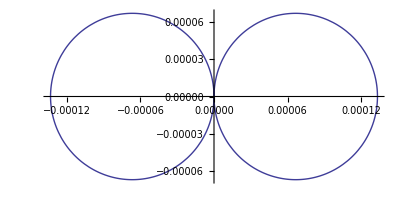

```mathematica
With[{lambda=1},With[{r=150 lambda,k=2 Pi/lambda,eta=120 Pi,I0=1,l=0.05 lambda},PolarPlot[Abs[Edipoler[r,theta,k,eta,l,I0]],{theta,-Pi,Pi}]]]
```

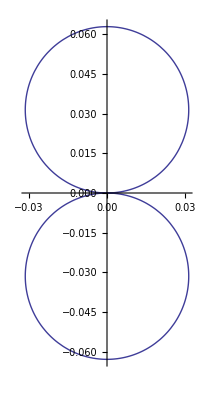

```mathematica
With[{lambda=1},With[{r=150 lambda,k=2 Pi/lambda,eta=120 Pi,I0=1,l=0.05 lambda},PolarPlot[Abs[Edipoletheta[r,theta,k,eta,l,I0]],{theta,-Pi,Pi}]]]
```

```mathematica
numberOfModes=5
```

5

```mathematica
phiArray={0}
```

{0}

```mathematica
thetaArray=Table[theta Degree,{theta,-60,60,1}];
```

```mathematica
deltaPhi=1
```

1

```mathematica
deltaTheta=1 Degree
```

°

```mathematica
EpthetaArray=With[{lambda=1},With[{r=10 lambda,k=2 Pi/lambda,eta=120 Pi,I0=1,l=0.05 lambda},Edipoletheta[r,thetaArray,k,eta,l,I0]]];
```

```mathematica
Length[thetaArray]
```

121

```mathematica
EpphiArray=Table[0,{Length[thetaArray]}];
```

```mathematica
wthetaData=With[{lambda=1},With[{k=2 Pi/lambda,eta=120 Pi},wfunc[k,eta,EpthetaArray]]];
```

```mathematica
wphiData=With[{lambda=1},With[{k=2 Pi/lambda,eta=120 Pi},wfunc[k,eta,EpphiArray]]];
```

```mathematica
N[With[{lambda=1},With[{r=100 lambda,thetas=30 Degree,phis=20 Degree,k=2 Pi/lambda,eta=120 Pi,numberOfModes=20},Efarfield[r,thetas,phis,k,eta,EpthetaArray,EpphiArray,thetaArray,phiArray,deltaTheta,deltaPhi,numberOfModes]]]]
```

{2.65383×10^-22+5.39481×10^-23 ⅈ,1.78312×10^-18+8.76224×10^-18 ⅈ,8.23267×10^-20-6.47511×10^-20 ⅈ}

#### Comprobación del campo obtenido con el teórico

```mathematica
EdipolerFarField[r_,theta_,k_,eta_,l_,I0_]:=eta I0 l Cos[theta]/(2 Pi r^2)  Exp[-I k r]
EdipolethetaFarField[r_,theta_,k_,eta_,l_,I0_]:=I eta k I0 l Sin[theta]/(4 Pi r)  Exp[-I k r]

thetaArray=Table[theta Degree,{theta,-60,60,1}];

EdipolethetaFarField[100,30 Degree,2 Pi,120 Pi,1,0.05 ]
```

0.+0.0471239 ⅈ